# Sophia’s MCRM Chaos Game Code!

Here’s the fractal function! It takes in 4 parameters:
- k is the list containing the scaling matrix for each vertex
- tf contains the transformation matrices (like rotation or reflection)
- tl contains the translation matrices
- n is a single positive integer, the number of iterations performed. The default value is 50000

```mathematica
Fractal[k_,tf_,tl_,n_:50000]:=(
p={RandomReal[],RandomReal[]};
allPoints={p};
For[i=1,i<=n,i++,
r=RandomInteger[{1,Length[k]}];
p=tf[[r]].(k[[r]].p)+tl[[r]];
allPoints=Append[allPoints,p]];
ListPlot[allPoints,AspectRatio->Automatic,PlotStyle->PointSize[0.001]]
)
```

Here’s an example using a familiar fractal from class!

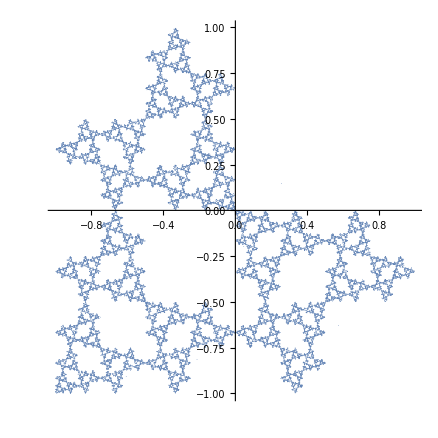

```mathematica
Fractal[
{{{1/2,0},{0,1/2}},
{{1/2,0},{0,1/2}},
{{1/2,0},{0,1/2}}},
{{{0,-1},{1,0}},
{{1,0},{0,1}},
{{0,1},{-1,0}}},
{{-1/2,1/2},
{-1/2,-1/2},
{1/2,-1/2}}]
```

I decided to use this to make fractals of words. Here’s a proof of concept I first did with my name.

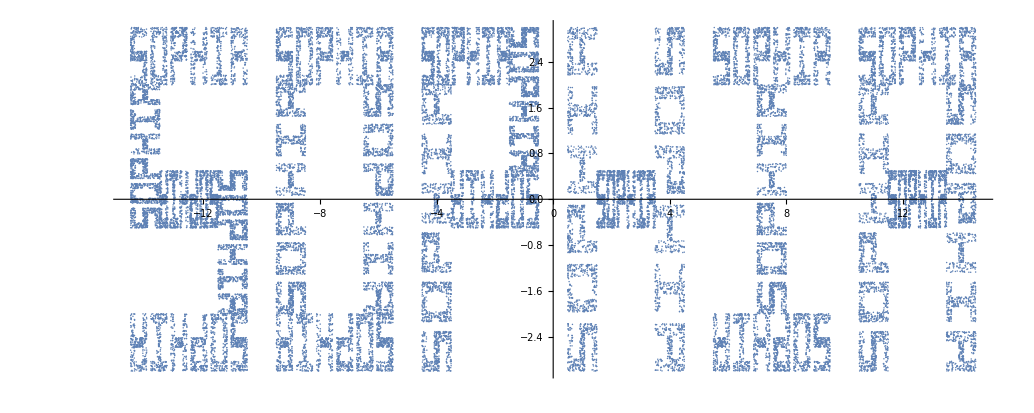

```mathematica
Fractal[
{{{4/29,0},{0,1/6}},
{{2.5/29,0},{0,1/6}},
{{2/29,0},{0,1/6}},
{{2.5/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},

{{4/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},

{{3/29,0},{0,1/6}},
{{2.5/29,0},{0,1/6}},
{{3/29,0},{0,1/6}},
{{5/29,0},{0,1/6}},

{{6/29,0},{0,1/6}},
{{2/29,0},{0,1/6}},
{{6/29,0},{0,1/6}},

{{4/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},

{{5/29,0},{0,1/6}},
{{4/29,0},{0,1/6}},
{{5/29,0},{0,1/6}},
{{2/29,0},{0,1/6}}},


{{{1,0},{0,1}},
{{0,-1},{1,0}},
{{-1,0},{0,-1}},
{{0,1},{-1,0}},
{{-1,0},{0,-1}},

{{1,0},{0,1}},
{{0,1},{-1,0}},
{{-1,0},{0,-1}},
{{0,-1},{1,0}},

{{1,0},{0,1}},
{{0,1},{-1,0}},
{{-1,0},{0,-1}},
{{0,-1},{1,0}},

{{0,-1},{1,0}},
{{1,0},{0,1}},
{{0,1},{-1,0}},

{{1,0},{0,1}},
{{0,-1},{1,0}},
{{-1,0},{0,-1}},

{{0,-1},{1,0}},
{{1,0},{0,1}},
{{0,1},{-1,0}},
{{1,0},{0,1}}},


{{-12.5,2.5},
{-14,0.75},
{-12.5,0},
{-11,-0.75},
{-12.5,-2.5},

{-7.5,2.5},
{-6,0},
{-7.5,-2.5},
{-9,0},

{-3,2.5},
{-1,1.75},
{-2,0},
{-4,-0.5},

{1,0},
{2.5,0},
{4,0},

{7.5,2.5},
{7.5,0},
{7.5,-2.5},

{11,-0.5},
{12.5,2.5},
{14,-0.5},
{12.5,0}},

50000]
```

I wanted to be able to make a fractal of any word, so I needed to adapt the code. First, I defined the function R(x) for the transformation matrix of x degrees counterclockwise rotation and then wrote out all of the transformations for letters A-Z in alphabetical order in the form:
{list of scale factors for horizontal stretch (all vertical scaling is just 1/6) for each vertex, list of R(degrees of counterclockwise rotation) for each vertex, list of translation matrices for each vertex}

```mathematica
R[x_]:={{Cos[x*Degree],-Sin[x*Degree]},{Sin[x*Degree],Cos[x*Degree]}}
letters={
{{5,4,5,2},{90,0,-90,0},{{-1.5,-0.5},{0,2.5},{1.5,-0.5},{0,0}}},
{{4,3,2.5,2,2.5,3},{90,0,-90,0,-90,180},{{-1.5,0},{-0.5,2.5},{1.5,1.75},{0,0},{1.5,-1.75},{-0.5,-2.5}}},
{{2,3,4,3,2},{-90,0,90,-180,-90},{{1.5,2},{-0.5,2.5},{-1.5,0},{-0.5,-2.5},{1.5,-2}}},
{{4,3,4,3},{90,0,-90,180},{{-1.5,0},{-0.5,2.5},{1.5,0},{-0.5,-2.5}}},
{{4,4,3,4},{90,0,0,0},{{-1.5,0},{0,2.5},{0.5,0},{0,-2.5}}},
{{5,4,3},{90,0,0},{{-1.5,-0.5},{0,2.5},{0.5,0}}},
{{4,4,3,2.5,2},{0,90,180,-90,0},{{0,2.5},{-1.5,0},{-0.5,-2.5},{1.5,-1.75},{1,0}}},
{{6,6,2},{90,-90,0},{{-1.5,0},{1.5,0},{0,0}}},
{{4,4,4},{0,90,0},{{0,2.5},{0,0},{0,-2.5}}},
{{5,3,2},{-90,180,90},{{1.5,0.5},{0.5,-2.5},{-1.5,-2}}},
{{6,2.5,2,2.5},{90,-90,0,-90},{{-1.5,0},{1.5,1.75},{0,0},{1.5,-1.75}}},
{{5,4},{90,0},{{-1.5,0.5},{0,-2.5}}},
{{6,6,2,2},{90,-90,0,90},{{-1.5,0},{1.5,0},{0,1},{0,-0.5}}},
{{6,2,2,6},{90,90,-90,-90},{{-1.5,0},{-0.5,0.5},{0.5,-0.5},{1.5,0}}},
{{4,4,4,4},{0,90,180,-90},{{0,2.5},{-1.5,0},{0,-2.5},{1.5,0}}},
{{5,3,2.5,3},{90,0,-90,180},{{-1.5,-0.5},{-0.5,2.5},{1.5,1.75},{0.5,0}}},
{{3.5,4,4,4},{0,90,180,-90},{{-0.25,2.5},{-1.5,0},{-0.25,-2.5},{1,0}}},
{{5,3,2.5,2,2.5},{90,0,-90,0,-90},{{-1.5,-0.5},{-0.5,2.5},{1.5,1.75},{0,0},{1.5,-1.75}}},
{{4,2.5,2,2.5,4},{0,90,0,-90,-180},{{0,2.5},{-1.5,0.75},{0,0},{1.5,-0.75},{0,-2.5}}},
{{4,5},{0,90},{{0,2.5},{0,-0.5}}},
{{5,4,5},{90,180,-90},{{-1.5,0.5},{0,-2.5},{1.5,0.5}}},
{{5,2,5},{90,180,-90},{{-1.5,0.5},{0,-2.5},{1.5,0.5}}},
{{5,3,4,5},{90,180,90,-90},{{-1.5,0.5},{0,-2.5},{0,0},{1.5,0.5}}},
{{2.5,2.5,2,2.5,2.5},{90,-90,0,90,-90},{{-1.5,1.75},{1.5,1.75},{0,0},{-1.5,-1.75},{1.5,-1.75}}},
{{2,3,2,3},{90,180,-90,90},{{-1.5,2},{0,0.5},{1.5,2},{0,-1.5}}},
{{3,2,2,2,2,3},{0,-90,-90,90,90,180},{{-0.5,2.5},{1.5,2},{0.5,0.5},{-0.5,-0.5},{-1.5,-2},{0.5,-2.5}}}
}
```

{{{5,4,5,2},{90,0,-90,0},{{-1.5,-0.5},{0,2.5},{1.5,-0.5},{0,0}}},{{4,3,2.5,2,2.5,3},{90,0,-90,0,-90,180},{{-1.5,0},{-0.5,2.5},{1.5,1.75},{0,0},{1.5,-1.75},{-0.5,-2.5}}},{{2,3,4,3,2},{-90,0,90,-180,-90},{{1.5,2},{-0.5,2.5},{-1.5,0},{-0.5,-2.5},{1.5,-2}}},{{4,3,4,3},{90,0,-90,180},{{-1.5,0},{-0.5,2.5},{1.5,0},{-0.5,-2.5}}},{{4,4,3,4},{90,0,0,0},{{-1.5,0},{0,2.5},{0.5,0},{0,-2.5}}},{{5,4,3},{90,0,0},{{-1.5,-0.5},{0,2.5},{0.5,0}}},{{4,4,3,2.5,2},{0,90,180,-90,0},{{0,2.5},{-1.5,0},{-0.5,-2.5},{1.5,-1.75},{1,0}}},{{6,6,2},{90,-90,0},{{-1.5,0},{1.5,0},{0,0}}},{{4,4,4},{0,90,0},{{0,2.5},{0,0},{0,-2.5}}},{{5,3,2},{-90,180,90},{{1.5,0.5},{0.5,-2.5},{-1.5,-2}}},{{6,2.5,2,2.5},{90,-90,0,-90},{{-1.5,0},{1.5,1.75},{0,0},{1.5,-1.75}}},{{5,4},{90,0},{{-1.5,0.5},{0,-2.5}}},{{6,6,2,2},{90,-90,0,90},{{-1.5,0},{1.5,0},{0,1},{0,-0.5}}},{{6,2,2,6},{90,90,-90,-90},{{-1.5,0},{-0.5,0.5},{0.5,-0.5},{1.5,0}}},{{4,4,4,4},{0,90,180,-90},{{0,2.5},{-1.5,0},{0,-2.5},{1.5,0}}},{{5,3,2.5,3},{90,0,-90,180},{{-1.5,-0.5},{-0.5,2.5},{1.5,1.75},{0.5,0}}},{{3.5,4,4,4},{0,90,180,-90},{{-0.25,2.5},{-1.5,0},{-0.25,-2.5},{1,0}}},{{5,3,2.5,2,2.5},{90,0,-90,0,-90},{{-1.5,-0.5},{-0.5,2.5},{1.5,1.75},{0,0},{1.5,-1.75}}},{{4,2.5,2,2.5,4},{0,90,0,-90,-180},{{0,2.5},{-1.5,0.75},{0,0},{1.5,-0.75},{0,-2.5}}},{{4,5},{0,90},{{0,2.5},{0,-0.5}}},{{5,4,5},{90,180,-90},{{-1.5,0.5},{0,-2.5},{1.5,0.5}}},{{5,2,5},{90,180,-90},{{-1.5,0.5},{0,-2.5},{1.5,0.5}}},{{5,3,4,5},{90,180,90,-90},{{-1.5,0.5},{0,-2.5},{0,0},{1.5,0.5}}},{{2.5,2.5,2,2.5,2.5},{90,-90,0,90,-90},{{-1.5,1.75},{1.5,1.75},{0,0},{-1.5,-1.75},{1.5,-1.75}}},{{2,3,2,3},{90,180,-90,90},{{-1.5,2},{0,0.5},{1.5,2},{0,-1.5}}},{{3,2,2,2,2,3},{0,-90,-90,90,90,180},{{-0.5,2.5},{1.5,2},{0.5,0.5},{-0.5,-0.5},{-1.5,-2},{0.5,-2.5}}}}

Here’s a test I ran of the entire alphabet.

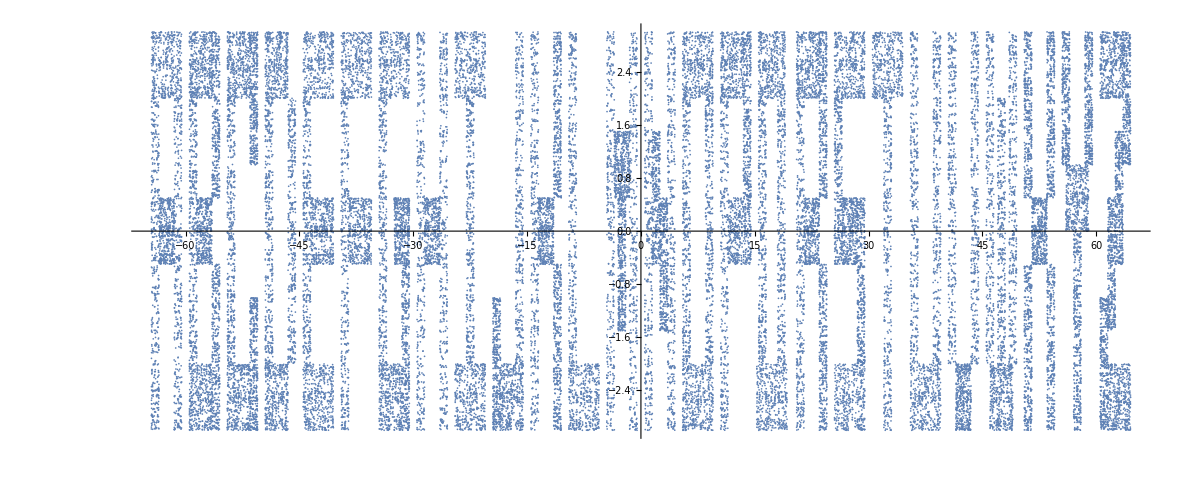

```mathematica
Fractal[
Map[List[{#/129,0},{0,1/6}]&,Flatten[Array[letters[[#]][[1]]&,26]]],
Map[R[#]&,Flatten[Array[letters[[#]][[2]]&,26]]],
Flatten[Array[letters[[#]][[3]]+ConstantArray[{-(5*26-1)/2-3+5#,0},Length[letters[[#]][[3]]]]&,26],1],
50000
]
```

I then adapted this code to make it generate any word the user inputs. it applies the transformations defined above in the letters variable to each letter in the inputted word. Just change the word variable!

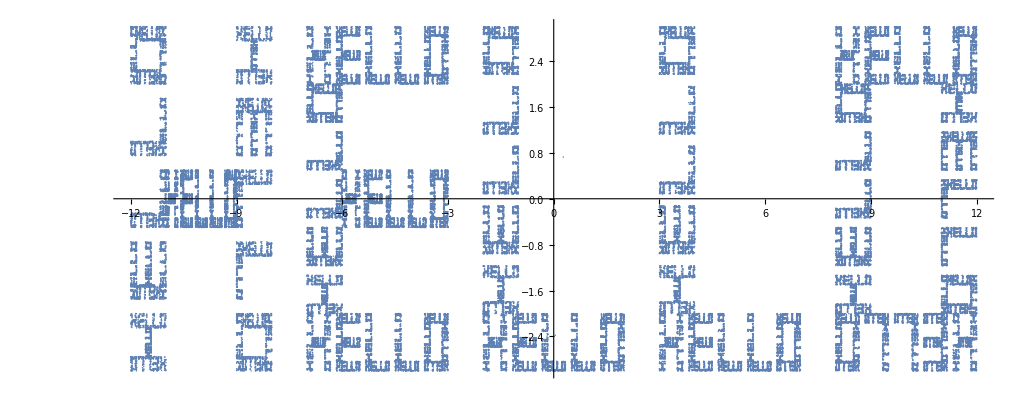

```mathematica
word:="hello"
chars:=Map[LetterNumber,Characters[word]]
len:=StringLength[word]
width:=5*len-1
Fractal[
Map[List[{#/width,0},{0,1/6}]&,Flatten[Array[letters[[chars[[#]]]][[1]]&,len]]],
Map[R[#]&,Flatten[Array[letters[[chars[[#]]]][[2]]&,len]]],
Flatten[Array[letters[[chars[[#]]]][[3]]+ConstantArray[{-width/2-3+5#,0},Length[letters[[chars[[#]]]][[3]]]]&,len],1],
100000
]
```

Calculating the fractal dimension for this example (“hello”):
The fractal has lots of different scale and stretch factors, so it is difficult to directly calculate the dimension. I’ll approximate it using the box method instead.
Let rf be the dimension of the gridlines. I will draw gridlines and count the number of boxes with the border within them, then use a line of best fit to approximate the dimension.

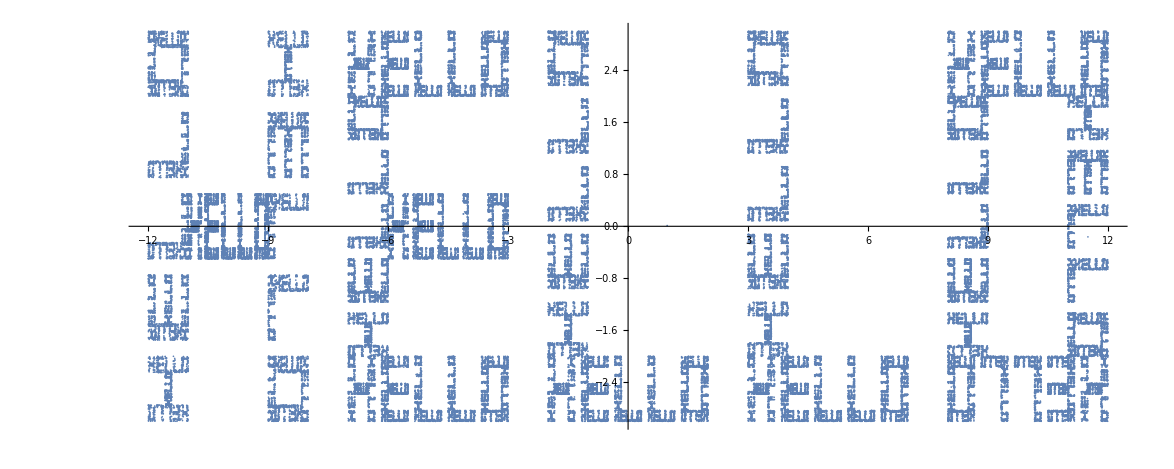

```mathematica
rf:=24
word:="hello"
chars:=Map[LetterNumber,Characters[word]]
len:=StringLength[word]
width:=5*len-1
Show[Fractal[
Map[List[{#/width,0},{0,1/6}]&,Flatten[Array[letters[[chars[[#]]]][[1]]&,len]]],
Map[R[#]&,Flatten[Array[letters[[chars[[#]]]][[2]]&,len]]],
Flatten[Array[letters[[chars[[#]]]][[3]]+ConstantArray[{-width/2-3+5#,0},Length[letters[[chars[[#]]]][[3]]]]&,len],1],
100000
],GridLines->{Range[-width/2,width/2,width/rf],Range[-3,3,6/rf]}]
```

Here is the recorded data in the form of {{rf_1, n_1,}, {rf_2,n_2}, ...} and the fitted model:

{{4,16},{8,56},{12,42},{16,170},{24,244}}

{{1.38629,2.77259},{2.07944,4.02535},{2.48491,3.73767},{2.77259,5.1358},{3.17805,5.49717}}

FittedModel[0.656673+1.5028 x]

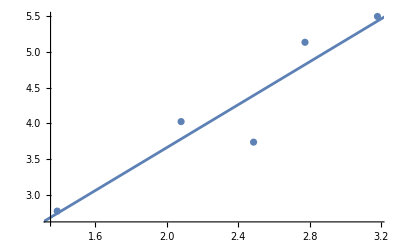

```mathematica
data={{4,16},{8,56},{12,42},{16,170},{24,244}}
data=N[Log[data]]
fit = LinearModelFit[data, x, x]
Show[ListPlot[data],Plot[fit[x],{x,0,25}]]
```

Thus, the fractal dimension is approximately 0.6567.

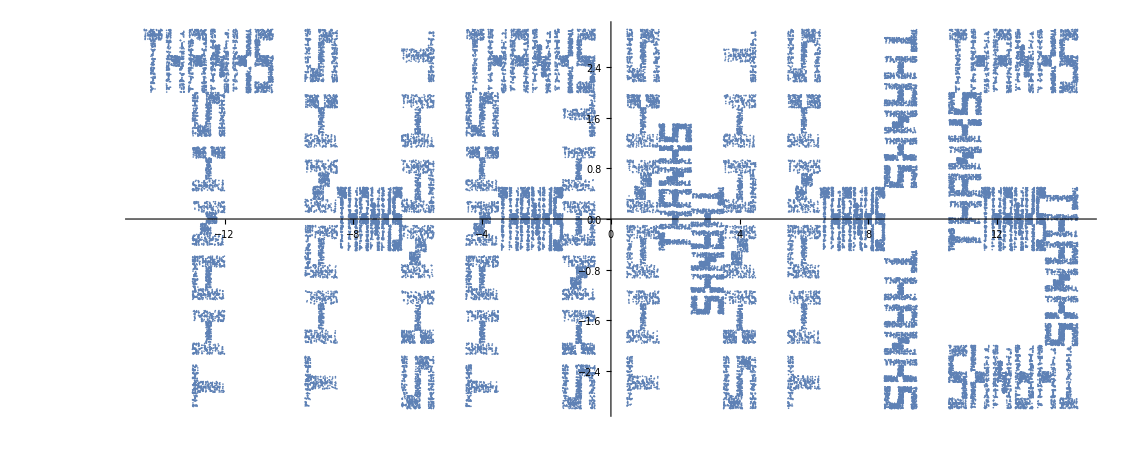

```mathematica
word:="thanks"
chars:=Map[LetterNumber,Characters[word]]
len:=StringLength[word]
width:=5*len-1
Fractal[
Map[List[{#/width,0},{0,1/6}]&,Flatten[Array[letters[[chars[[#]]]][[1]]&,len]]],
Map[R[#]&,Flatten[Array[letters[[chars[[#]]]][[2]]&,len]]],
Flatten[Array[letters[[chars[[#]]]][[3]]+ConstantArray[{-width/2-3+5#,0},Length[letters[[chars[[#]]]][[3]]]]&,len],1],
100000
]
```